## Space-time Metric Round a Rotating Matter

##### Kim Mingi(xp2425@khu.ac.kr)

Einstein field equation: R_μν-1/2 g_μν R=(8πG)/c^2 T_μν , R_μν=(8πG)/c^2(T_μν-1/2 g_μν T)

Conservation law of special relativity: (T^μν)_(;ν)=0 (continuity equation)

Components in T^μν: (T^00: | energy density
T^(0k) | flow of energy along x^k   , (T^(m 0)/c: | density of  m th comp. of momentum (p^m)
T^(m n): | flow of p^m along x^n

Conservation equations

1/c(∂T^00)/(∂t)+(∂T^m0)/(∂x^m)=0  ,  1/c(∂T^m0)/(∂t)+(∂T^mn)/(∂x^m)=0

T^μν is a symmetric tensor ⧦ flow of energy is equivalent to density of momentum

T^μν=ρ (1 | v_x/c | v_y/c | v_z/c
v_x/c | v_x^2/c^2 | v_x v_y/c^2 | v_x v_z/c^2
v_y/c | v_y v_x/c^2 | v_y^2/c^2 | v_y v_z/c^2
v_z/c | v_z v_x/c^2 | v_z v_y/c^2 | v_z^2/c^2)

### 1. Weak Field Limit

For a weak gravitational field (h_μν<<1), the metric is near the Minkowski metric, η_(μ ν)

g_μν=η_μν+h_μν , h_μν<<1

Assume that g^μν=η^μν+χ^μν, χ^μν<<1. Then from g^μν g_νρ=(δ^μ)_ρ,

(δ^μ)_ρ=(η^μν+χ^μν)(η_νρ+h_νρ)=(δ^μ)_ρ+(χ^μ)_ρ+(h^μ)_ρ+𝒪

Namely, g^μν=η^μν-h^μν   In short, -(g_μν=η_μν+h_μν
g^μν=η^μν-h^μν

Recall that Christoffel symbol and Ricci tensor are given by

(Γ^κ)_λμ=1/2 g^κρ(g_(ρλ ,μ)+g_(ρμ ,λ)-g_(λμ ,ρ))

R_μν=(Γ^κ)_(μν,κ)-(Γ^κ)_(μκ,ν)+(Γ^κ)_ρκ(Γ^ρ)_μν-(Γ^κ)_ρν(Γ^ρ)_μκ

In this case, they are given

(Γ^κ)_λμ=1/2(η^κρ-h^κρ)(h_(ρλ ,μ)+h_(ρμ ,λ)-h_(λμ ,ρ))=1/2 η^κρ(h_(ρλ ,μ)+h_(ρμ ,λ)-h_(λμ ,ρ))+𝒪(h^2) =1/2 η^κρ(h_(ρλ ,μ)+h_(ρμ ,λ)-h_(λμ ,ρ))

R_μν=(Γ^κ)_(μν,κ)-(Γ^κ)_(μκ,ν)+(Γ^κ)_ρκ(Γ^ρ)_μν-(Γ^κ)_ρν(Γ^ρ)_μκ
=(Γ^κ)_(μν,κ)-(Γ^κ)_(μκ,ν)+𝒪 (h^2)
=1/2 η^κρ(h_(ρν ,μκ)+h_(ρμ ,νκ)-h_(μν ,ρκ))-1/2 η^κρ(h_(ρμ ,κν)+h_(ρκ ,μν)-h_(μκ ,ρν))
=1/2(η^κρ h_(ρν ,μκ)-η^κρ h_(ρκ ,μν)-η^κρ h_(μν ,ρκ)+η^κρ h_(μκ ,ρν))
=1/2(η^κρ h_(ρν ,μκ)+η^κρ h_(μκ ,ρν)-η^κρ h_(ρκ ,μν)-□h_μν)

R_μν=1/2(η^κρ h_(ρν ,μκ)+η^κρ h_(μκ ,ρν)-η^κρ h_(ρκ ,μν)-□h_μν)

note that η^μν∂_μ ∂_ν is a D’Alembertian ‘□’

From Einstein field equation, (S_μν=T_μν-1/2 g_μν T)

R_μν=(8 πG)/c^2(T_μν-1/2 g_μν T)=1/2(η^κρ h_(ρν ,μκ)+η^κρ h_(μκ ,ρν)-η^κρ h_(ρκ ,μν)-□h_μν)

(16πG)/c^2 S_μν=η^κρ h_(ρν ,μκ)+η^κρ h_(μκ ,ρν)-η^κρ h_(ρκ ,μν)-□h_μν

To express in neater way define new quantities, f^μν

√-g g^μν=η^μν-f^μν

where g=det(g_μν),  g_μν=η_μν+h_μν

```mathematica
η:=DiagonalMatrix[{-1,1,1,1}];
H:=Table[Subscript[h,i,j],{i,0,3},{j,0,3}];
η+H//MatrixForm//TraditionalForm
```

(h_(0,0)-1 | h_(0,1) | h_(0,2) | h_(0,3)
h_(1,0) | h_(1,1)+1 | h_(1,2) | h_(1,3)
h_(2,0) | h_(2,1) | h_(2,2)+1 | h_(2,3)
h_(3,0) | h_(3,1) | h_(3,2) | h_(3,3)+1)

so,

g=(-1+h_00)(1+h_11)(1+h_22)(1+h_22)+𝒪 (h^2)
=-1+h_00-h_11-h_22-h_33+𝒪 (h^2)
=-1+η_00(h^0)_0-η_11(h^1)_1-η_22(h^2)_2-η_33(h^3)_3+𝒪 (h^2)
=-1-(h^0)_0-(h^1)_1-(h^2)_2-(h^3)_3+𝒪 (h^2)
=-1-(h^μ)_μ+𝒪 (h^2)

hence,

√-g=(-g)^(1/2)=(1+(h^λ)_λ+𝒪 (h^2))^(1/2)=1+1/2(h^μ)_μ+𝒪 (h^2)

√-g g^μν=(1+1/2(h^λ)_λ+𝒪 (h^2))(η^μν-h^μν)=η^μν-f^μν

η^μν+1/2 η^μν(h^λ)_λ-h^μν+𝒪 (h^2)=η^μν-f^μν

f^μν=h^μν-1/2 η^μν(h^λ)_λ

η_μν f^μν=(f^μ)_μ=η_μν(h^μν-1/2 η^μν(h^λ)_λ)=(h^μ)_μ-1/2(4)(h^λ)_λ=-(h^μ)_μ

f^μν=h^μν-1/2η^μν(-(f^λ)_λ) ⟶  h^μν=f^μν-1/2 η^μν(f^λ)_λ

(h^λ)_ν=η_μν h^μλ=η_μν(f^μλ-1/2 η^μλ(f^ρ)_ρ)=(f^λ)_ν-1/2(η^λ)_ν(f^ρ)_ρ

h_μν=η_λμ(h^λ)_ν=η_λμ((f^λ)_ν-1/2(η^λ)_ν(f^ρ)_ρ)=f_μν-1/2 η_μν(f^ρ)_ρ

Now back to the field equation.

R_μν=1/2(η^κρ h_(ρν ,μκ)+η^κρ h_(μκ ,ρν)-η^κρ h_(ρκ ,μν)-□h_μν)=(8πG)/c^2 T_μν

((h^λ)_(ν ,μλ)+(h^λ)_(μ ,λν)-(h^λ)_(λ ,μν)-□h_μν)

⇒[((f^λ)_ν-1/2(η^λ)_ν(f^ρ)_ρ)_(,μλ)+((f^λ)_μ-1/2(η^λ)_μ(f^ρ)_ρ)_(,λν)-(-(f^ρ)_ρ)_(,μν)-□(f_μν-1/2 η_μν(f^ρ)_ρ)]

=[((f^λ)_ν)_(,μλ)+((f^λ)_μ)_(,λν)-((f^ρ)_ρ)_(,μν)+((f^ρ)_ρ)_(,μν)-□f_μν+1/2 η_μν□(f^ρ)_ρ]=[((f^λ)_ν)_(,μλ)+((f^λ)_μ)_(,λν)-□f_μν+1/2 η_μν□(f^ρ)_ρ]

f has to be independent of time. Finally,

R_μν=1/2 [((f^λ)_ν)_(,μλ)+((f^λ)_μ)_(,λν)-□f_μν+1/2 η_μν□(f^ρ)_ρ]

and

(1/2)η_μν R=(1/2)η_μν(η^ρσ R_ρσ)
=(1/2)η_μν η^ρσ(1/2)[((f^λ)_σ)_(,ρλ)+((f^λ)_ρ)_(,σν)-□f_ρσ+1/2 η_ρσ□(f^λ)_λ]
=(1/4)η_μν [(f^λρ)_(,ρλ)+(f^λσ)_(,σν)-□(f^λ)_λ+1/2(4)□(f^λ)_λ]
=1/4 η_μν[2(f^λρ)_(,ρλ)+□(f^λ)_λ]=1/2 η_μν(f^ρσ)_(,ρσ)+1/4 η_μν□(f^λ)_λ

Then the field equation R_μν-1/2 g_μν R=(8πG)/c^2 T_μν give

1/2 [((f^λ)_ν)_(,μλ)+((f^λ)_μ)_(,λν)-□f_μν+1/2 η_μν□(f^ρ)_ρ]-(1/2 η_μν(f^ρσ)_(,ρσ)+1/4 η_μν□(f^λ)_λ)

=1/2 [((f^λ)_ν)_(,μλ)+((f^λ)_μ)_(,λν)-η_μν(f^ρσ)_(,ρσ)-□f_μν]=(8πG)/c^2 T_μν

((f^λ)_ν)_(,μλ)+((f^λ)_μ)_(,λν)-η_μν(f^ρσ)_(,ρσ)-□f_μν=(16πG)/c^2 T_μν

By choosing proper transformation, we can simplify above equation.

x^μ ⟶y^μ=x^μ+b^μ(x)

Under given transformation,

(∂y^μ)/(∂x^ν)=(δ^μ)_ν+(b^μ)_(,ν)

g^μν(x)⟶g'^μν(y)=(∂y^μ)/(∂x^ρ)(∂y^ν)/(∂x^σ)g^ρσ(x)=((δ^μ)_ρ+(b^μ)_(,ρ))((δ^ν)_σ+(b^ν)_(,σ))g^ρσ

=((δ^μ)_ρ+(b^μ)_(,ρ))(g^ρν+g^ρσ(b^ν)_(,σ))=g^μν+g^ρν(b^μ)_(,ρ)+g^μσ(b^ν)_(,σ)+𝒪 (b^2)

Then the transformed metric tensor g'^μν is given as below.

```mathematica
Table[g^ToString[{i,j}]+g^("ρ" ToString[j])Subscript[(b^ToString[i]), ",ρ"]+g^(ToString[i]"ρ")Subscript[(b^ToString[j]), ",ρ"],
{i,0,3},{j,0,3}]//MatrixForm//TraditionalForm
```

(2 (b^0)_(,ρ) g^(0 ρ)+g^{0, 0} | g^(0 ρ) (b^1)_(,ρ)+(b^0)_(,ρ) g^(1 ρ)+g^{0, 1} | g^(0 ρ) (b^2)_(,ρ)+(b^0)_(,ρ) g^(2 ρ)+g^{0, 2} | g^(0 ρ) (b^3)_(,ρ)+(b^0)_(,ρ) g^(3 ρ)+g^{0, 3}
g^(0 ρ) (b^1)_(,ρ)+(b^0)_(,ρ) g^(1 ρ)+g^{1, 0} | 2 (b^1)_(,ρ) g^(1 ρ)+g^{1, 1} | g^(1 ρ) (b^2)_(,ρ)+(b^1)_(,ρ) g^(2 ρ)+g^{1, 2} | g^(1 ρ) (b^3)_(,ρ)+(b^1)_(,ρ) g^(3 ρ)+g^{1, 3}
g^(0 ρ) (b^2)_(,ρ)+(b^0)_(,ρ) g^(2 ρ)+g^{2, 0} | g^(1 ρ) (b^2)_(,ρ)+(b^1)_(,ρ) g^(2 ρ)+g^{2, 1} | 2 (b^2)_(,ρ) g^(2 ρ)+g^{2, 2} | g^(2 ρ) (b^3)_(,ρ)+(b^2)_(,ρ) g^(3 ρ)+g^{2, 3}
g^(0 ρ) (b^3)_(,ρ)+(b^0)_(,ρ) g^(3 ρ)+g^{3, 0} | g^(1 ρ) (b^3)_(,ρ)+(b^1)_(,ρ) g^(3 ρ)+g^{3, 1} | g^(2 ρ) (b^3)_(,ρ)+(b^2)_(,ρ) g^(3 ρ)+g^{3, 2} | 2 (b^3)_(,ρ) g^(3 ρ)+g^{3, 3})

With g'=|g'_μν|=|g'^μν|^-1 ,

(g')^-1=|g'^μν|=(g^00+2 g^(0ρ) (b^0)_(,ρ))(g^11+2 g^(1ρ) (b^1)_(,ρ))(g^22+2 g^(2ρ) (b^2)_(,ρ))(g^33+2 g^(3ρ) (b^3)_(,ρ))+𝒪 (b^2)
=g^00 g^11 g^22 g^33+2(g^ρ0 g^11 g^22 g^33(b^0)_(,ρ)+g^00 g^ρ1 g^22 g^33(b^1)_(,ρ)+g^00 g^11 g^ρ2 g^33(b^2)_(,ρ)+g^00 g^11 g^22 g^ρ3(b^3)_(,ρ))+𝒪 (b^2)
=g^-1+2g^-1((b^0)_(,0)+(b^1)_(,1)+(b^2)_(,2)+(b^3)_(,3))=g^-1(1+2(b^λ)_(,λ))

Namely,

g'=g(1-2(b^λ)_(,λ)),  √-g'=√-g(1-(b^λ)_(,λ))

√-g' g'^μν=√-g(1-(b^λ)_(,λ))(g^μν+g^ρν(b^μ)_(,ρ)+g^μσ(b^ν)_(,σ))=√-g(g^μν+g^ρν(b^μ)_(,ρ)+g^μσ(b^ν)_(,σ)-g^μν(b^λ)_(,λ))+𝒪 (b^2)

=√-g(g^μν+g^ρν(b^μ)_(,ρ)+g^μσ(b^ν)_(,σ)-g^μν(b^λ)_(,λ))=η^μν-f'^μν

last term come from  √-g g^μν=η^μν-f^μν

√-g(g^μν+g^ρν(b^μ)_(,ρ)+g^μσ(b^ν)_(,σ)-g^μν(b^λ)_(,λ))=η^μν-f'^μν

η^μν-f^μν+(η^ρν-f^ρν)(b^μ)_(,ρ)+(η^μσ-f^μσ)(b^ν)_(,σ)-(η^μν-f^μν)(b^λ)_(,λ)=η^μν-f'^μν

-f^μν+(η^ρν-f^ρν)(b^μ)_(,ρ)+(η^μσ-f^μσ)(b^ν)_(,σ)-(η^μν-f^μν)(b^λ)_(,λ)=-f'^μν

Hence,

f'^μν=f^μν-η^ρν(b^μ)_(,ρ)-η^μσ(b^ν)_(,σ)+η^μν(b^λ)_(,λ)

and,

(f'^μν)_(,ν)=(f^μν)_(,ν)-η^ρν(b^μ)_(,ρν)-η^μσ(b^ν)_(,σν)+η^μν(b^λ)_(,λν)=(f^μν)_(,ν)-η^ρν(b^μ)_(,ρν)=(f^μν)_(,ν)-□b^μ

where η^ρν∂_ρ ∂_ν is a D’Alembertian ‘□’. So we can properly choose b^μ such that (f^μν)_(,ν)=□b^μ , so that (f'^μν)_(,ν)=0  or,

(√-g' g'^μν)_(,ν)=0    (harmonic condition)

Under the harmonic condition,

((f^λ)_ν)_(,μλ)+((f^λ)_μ)_(,λν)-η_μν(f^ρσ)_(,ρσ)-□f_μν=(16πG)/c^2 T_μν ⟹ -□f_μν=(16πG)/c^2 T_μν

Finally the field equation reduced to the following Poisson equation

□f_μν=-(16πG)/c^2 T_μν

with harmonic condition

(f^μν)_(,ν)=(√-g g^μν)_(,ν)=0

where

(f^μν=h^μν-1/2 η^μν(h^λ)_λ
g_μν=η_μν+h_μν=η_μν+f_μν-1/2 η_μν(f^λ)_λ
g^μν=η^μν-h^μν=η_μν-f_μν+1/2 η_μν(f^λ)_λ
(f^λ)_λ=η^μλ f_μλ=-f_00+f_11+f_22+f_33

We already dealt with the Poisson’s equation at Electromagnetism course (see Griffith’s book chap 10.2); solution of the equation (13)  is given by

f_μν(r,t)=1/(4π)(16πG)/c^2∫ (T_μν(r',t_r))/𝕣 ⅆτ

where t_r (retarded time) =t-𝕣/c and  𝕣=r-r',  𝕣=|r-r'|

### 2. Rotating Body: Angular Momentum

Consider a body rotating with constant angular velocity ω=ⅆϕ/ⅆt about the x^3-axis (z axis) and assume that v<<c. Then,

T^μν=ρ (1 | v_x/c | v_y/c | v_z/c
v_x/c | v_x^2/c^2 | v_x v_y/c^2 | v_x v_z/c^2
v_y/c | v_y v_x/c^2 | v_y^2/c^2 | v_y v_z/c^2
v_z/c | v_z v_x/c^2 | v_z v_y/c^2 | v_z^2/c^2)=ρ (1 | v_x/c | v_y/c | 0
v_x/c | 0 | 0 | 0
v_y/c | 0 | 0 | 0
0 | 0 | 0 | 0)

T_μν=η_μλ η_νρ T^λρ=ρ (1 | -v_x/c | -v_y/c | 0
-v_x/c | 0 | 0 | 0
-v_y/c | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Show[Graphics3D[{{Opacity[0.4],Cylinder[{{2,1,0},{2,1,1.5}},0.8]},PointSize[0.02],Point@{{0,0,0},{2.1,1.4,1.2},{2,4,2}},Line[{{0,0,0},{2.1,1.4,1.2},{2,4,2},{0,0,0}}],Text["O",{0,0.2,0.2}],Text["Q(X,Y,Z)",{2.3,1.6,1.2}],Text["P(x,y,z)",{2,4,2.2}],Text["R",{1.2,0.9,0.7}],Text["r",{1,2.1,1.2}]}],Boxed->False,Axes->True,AxesOrigin->{0,0,0}]
```

-Graphics3D-

As above figure, let’s call the coordinates of a point Q (object) inside the rotating body by X^i and those of a point P (observer) outside the body by x^i then, (r^2=x^i x_i
R^2=X^i X_i  with  R<<r. Hence,

𝕣=|r-R|=(r^2-2r·R+R^2)^(1/2)=r (1-2(r·R)/r^2+R^2/r^2)^(1/2)≃r (1-(r·R)/r^2)

1/𝕣=|r-R|^-1=1/r(1+(r·R)/r^2)

The field equation (□f_μν=-(16πG)/c^2 T_μν ) gives  (□f_00=-(16πG)/c^2ρ
□f_01=-(16πG)/c^2 T_01
□f_02=-(16πG)/c^2 T_02   , other f_μν=0         ( recall that  (f^μν=h^μν-1/2 η^μν(h^λ)_λ
g_μν=η_μν+h_μν=η_μν+f_μν-1/2 η_μν(f^λ)_λ
g^μν=η^μν-h^μν=η_μν-f_μν+1/2 η_μν(f^λ)_λ
(f^λ)_λ=η^μλ f_μλ=-f_00+f_11+f_22+f_33))

then □f_00=-(16πG)/c^2ρ is analog to Newton’s equation: ∇^2 ϕ=-4πGρ  ⟶ f_00=(4ϕ)/c^2,   (f^λ)_λ=-f_00=-(4ϕ)/c^2

g_μν=η_μν+f_μν-1/2η_μν(-(4ϕ)/c^2)=f_μν+(1+(2ϕ)/c^2)η_μν

g_00=(4ϕ)/c^2-1-(2ϕ)/c^2=-(1-(2ϕ)/c^2)

```mathematica
F=Table[Subscript[f,i,j],{i,0,3},{j,0,3}];
F[[1,4]]=F[[4,1]]=0;F[[1,1]]=4ϕ/c^2;
F[[2;;4,2;;4]]=ConstantArray[0,{3,3}];F//MatrixForm//TraditionalForm
g:=F+(1+2ϕ/c^2)η;g//MatrixForm//TraditionalForm
```

((4 ϕ)/c^2 | f_(0,1) | f_(0,2) | 0
f_(1,0) | 0 | 0 | 0
f_(2,0) | 0 | 0 | 0
0 | 0 | 0 | 0)

((2 ϕ)/c^2-1 | f_(0,1) | f_(0,2) | 0
f_(1,0) | (2 ϕ)/c^2+1 | 0 | 0
f_(2,0) | 0 | (2 ϕ)/c^2+1 | 0
0 | 0 | 0 | (2 ϕ)/c^2+1)

where ϕ=GM/r+…,  As long as we get f_01 and f_02, then we can figure out the whole metric tensor g_μν. To get f_(0i) , (i=1,2) we have to utilize the solution of the Poisson’s equation (eq.(14)) we’ve already met.

f_μν(r,t)=1/(4π)(16πG)/c^2∫ (T_μν(r',t_r))/𝕣 ⅆτ

(f_01=(4G)/c^2∫1/𝕣 T_01 ⅆ^3 X=(4G)/(c^2 r)∫(1+(r·R)/r^2)T_01 ⅆ^3 X=(4G)/(c^2 r)[∫ T_01 ⅆ^3 X+x^i/r^2∫X_i T_01 ⅆ^3 X]
f_02=(4G)/c^2∫1/𝕣 T_02 ⅆ^3 X=(4G)/(c^2 r)∫(1+(r·R)/r^2)T_02 ⅆ^3 X=(4G)/(c^2 r)[∫ T_02 ⅆ^3 X+x^i/r^2∫X_i T_02 ⅆ^3 X]

Evaluating the integral ∫T_01 ⅆ^3 X is not that difficult. Since T_01=-(ρ v_x)/c=-ρ/c(ⅆ X^1)/ⅆt and the  quantity (ⅆ X^1)/ⅆt has two positive and two negative signs on circular motion, the value of integration reduced to zero.

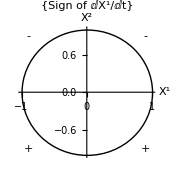

```mathematica
a=0.9;Show[Graphics[{Circle[],Text[Style["+",Large],{a,-a}],Text[Style["-",Large],{a,a}],Text[Style["-",Large],{-a,a}],Text[Style["+",Large],{-a,-a}]}],Axes->True,AxesOrigin->{0,0},AxesLabel->{X^("1"),X^("2")},PlotLabel->{"Sign of ⅆX^(<1>)/ⅆt"}]
```

(f_01=(4G)/(c^2 r)[x^i/r^2∫X_i T_01 ⅆ^3 X]
f_02=(4G)/(c^2 r)[x^i/r^2∫X_i T_02 ⅆ^3 X]

Then let’s consider the remaining integral ∫X_i T_01 ⅆ^3 X. Similarly, we can check the sign of  X_i T_01=X_i(ⅆ X^1)/ⅆt and kill some zeros.

i=1;  Sign of X_1(ⅆ X^1)/ⅆt

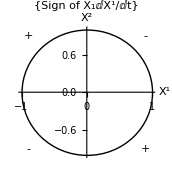

```mathematica
a=0.9;Show[Graphics[{Circle[],Text[Style["+",Large],{a,-a}],Text[Style["-",Large],{a,a}],Text[Style["+",Large],{-a,a}],Text[Style["-",Large],{-a,-a}]}],Axes->True,AxesOrigin->{0,0},AxesLabel->{X^("1"),X^("2")},PlotLabel->{"Sign of X_1ⅆX^(<1>)/ⅆt"}]
```

i=2 ; Sign of  X_2(ⅆ X^1)/ⅆt

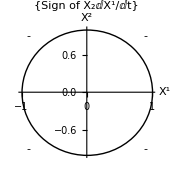

```mathematica
a=0.9;Show[Graphics[{Circle[],Text[Style["-",Large],{a,-a}],Text[Style["-",Large],{a,a}],Text[Style["-",Large],{-a,a}],Text[Style["-",Large],{-a,-a}]}],Axes->True,AxesOrigin->{0,0},AxesLabel->{X^("1"),X^("2")},PlotLabel->{"Sign of X_2ⅆX^(<1>)/ⅆt"}]
```

i=3 ; Sign of  X_3(ⅆ X^1)/ⅆt is equal to sign of (ⅆ X^1)/ⅆt, because X_3(=Z) is always positive in this situation.

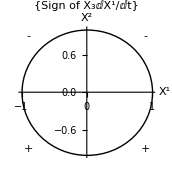

```mathematica
a=0.9;Show[Graphics[{Circle[],Text[Style["+",Large],{a,-a}],Text[Style["-",Large],{a,a}],Text[Style["-",Large],{-a,a}],Text[Style["+",Large],{-a,-a}]}],Axes->True,AxesOrigin->{0,0},AxesLabel->{X^("1"),X^("2")},PlotLabel->{"Sign of X_3ⅆX^(<1>)/ⅆt"}]
```

Thus, the only non-vanishing term is

(f_01=(4G)/(c^2 r)[x^2/r^2∫X_2 T_01 ⅆ^3 X]=(4G y)/(c^2 r^3)∫ Y T_01 ⅆ^3 X=-(4G y)/(c^2 r^3)∫ Y T^01 ⅆ^3 X
f_02=(4G)/(c^2 r)[x^1/r^2∫X_1 T_02 ⅆ^3 X]=(4G x)/(c^2 r^3)∫ X T_02 ⅆ^3 X=-(4G x)/(c^2 r^3)∫ X T^02 ⅆ^3 X

What is the meaning of above terms? Before we consider this, we need to talk about essential meaning of T^(0 m); do you remember?

T^(m 0)/c: | density of  m th comp. of momentum (p^m)

So the volume integral of the T^(m 0) must be the  m the component of momentum, p^m itself. Moreover, in special relativity, the angular momentum is denoted by

J=r×p, J^3=x^1 p^2-x^2 p^1

more generally,

J^3=∫(x^1 ⅆ p^2-x^2 ⅆ p^1)=c∫(x^1 T^02-x^2 T^01)ⅆτ

In this case,

J^3=c∫(X T^02-Y T^01)ⅆ^3 X

The conservation of angular momentum requires (∂ T^(i k))/(∂ x^k)=0 (in fact, it comes from the definition of energy-momentum tensor)

(Landau&Lifshitz) From the Lagrange’s e.o.m (essentially, conservation of energy) of generalized coordinate 𝓆 ,

∂/(∂x^i)(∂ℒ)/(∂q_(,i))- (∂ℒ)/(∂q)=0,  where  ℒ is a Lagrangian for this motion

Then, the derivative of Lagrangian is given by

(∂ℒ)/(∂x^i)=(∂ℒ)/(∂q)(∂q)/(∂x^i)+(∂ℒ)/(∂q_(,k))(∂q_(,k))/(∂x^i)=(∂/(∂x^k)(∂ℒ)/(∂q_(,k)))q_(,i)+(∂ℒ)/(∂q_(,k))q_(,k i)=∂/(∂x^k)((∂ℒ)/(∂q_(,k))q_(,i))

where we can write

(∂ℒ)/(∂x^i)=((δ^k)_i(∂ℒ)/(∂x^k))

Consequently,

((δ^k)_i(∂ℒ)/(∂x^k))=∂/(∂x^k)((∂ℒ)/(∂q_(,k))q_(,i)),  ∂/(∂x^k)((∂ℒ)/(∂q_(,k))q_(,i)-(δ^k)_i ℒ)=0

where (∂ℒ)/(∂q_(,k))q_(,i)-(δ^k)_i ℒ   is  called   (T^k)_i that (T^k)_(i ,k)=0

Remind the given energy momentum tensor.

T^μν=ρ (1 | v_x/c | v_y/c | 0
v_x/c | 0 | 0 | 0
v_y/c | 0 | 0 | 0
0 | 0 | 0 | 0)  ,     (T^μν)_(,ν) =0

For a static distribution (=time independent) of matter, (T^μ0)_(,0)=0, hence, with  μ=0,

(T^(0ν))_(,ν)=(T^00)_(,0)+(T^01)_(,1)+(T^02)_(,2)+(T^03)_(,3)=0  ⟹ (T^01)_(,1)+(T^02)_(,2)=0

It follows that

∫X^k X^m((T^01)_(,1)+(T^02)_(,2))ⅆ^3 X=0

∫X^k X^m((T^01)_(,1)+(T^02)_(,2))ⅆ^3 X=∫X^k X^m(T^(0i))_(,i)ⅆ^3 X
=∫[∂_i (X^k X^m T^(0i))-∂_i (X^k)X^m T^(0i)-X^k∂_i (X^m)T^(0i)]ⅆ^3 X
=∫[∂_i (X^k X^m T^(0i))-((δ^k)_i)X^m T^(0i)-X^k((δ^m)_i)T^(0i)]ⅆ^3 X
=∫[∂_i (X^k X^m T^(0i))-X^m T^(0k)-X^k T^(0m)]ⅆ^3 X=0

The first term can be rewritten as ∫ ∇·(X^k X^m T^0)ⅆτ=∮ (X^k X^m T^0)·ⅆa, the divergence theorem. Note that the income is equal to the outcome momentum. Namely, the divergence term vanishes. Therefore,

∫(X^m T^(0k)+X^k T^(0m))ⅆ^3 X=0 ⟹ ∫(X T^02+Y T^01)ⅆ^3 X=0

From above relation, it turns out that

∫Y T^01 ⅆ^3 X=-∫X T^02 ⅆ^3 X=1/2∫(Y T^01-X T^02)ⅆ^3 X=-J^3/(2c)

Last equality comes from the eq.(21). Finally,

(f_01=-(4G y)/(c^2 r^3)∫ Y T^01 ⅆ^3 X=-(4G y)/(c^2 r^3)(-J^3/(2c))=(2G)/c^3 y/r^3 J^3
f_02=-(4G x)/(c^2 r^3)∫ X T^02 ⅆ^3 X=-(4G x)/(c^2 r^3)(J^3/(2c))=-(2G)/c^3 x/r^3 J^3

```mathematica
F[[1,2]]=F[[2,1]]=(2G/c^3)(y/r^3)Subscript[J, z];
F[[1,3]]=F[[3,1]]=-(2G/c^3)(x/r^3)Subscript[J, z];F//MatrixForm//TraditionalForm
g//MatrixForm//TraditionalForm
```

((4 ϕ)/c^2 | (2 G y J_z)/(c^3 r^3) | -(2 G x J_z)/(c^3 r^3) | 0
(2 G y J_z)/(c^3 r^3) | 0 | 0 | 0
-(2 G x J_z)/(c^3 r^3) | 0 | 0 | 0
0 | 0 | 0 | 0)

((2 ϕ)/c^2-1 | (2 G y J_z)/(c^3 r^3) | -(2 G x J_z)/(c^3 r^3) | 0
(2 G y J_z)/(c^3 r^3) | (2 ϕ)/c^2+1 | 0 | 0
-(2 G x J_z)/(c^3 r^3) | 0 | (2 ϕ)/c^2+1 | 0
0 | 0 | 0 | (2 ϕ)/c^2+1)

In linear approximation, (ϕ≃ GM/r)

```mathematica
g/.ϕ->G M/r//MatrixForm//TraditionalForm
```

((2 G M)/(c^2 r)-1 | (2 G y J_z)/(c^3 r^3) | -(2 G x J_z)/(c^3 r^3) | 0
(2 G y J_z)/(c^3 r^3) | (2 G M)/(c^2 r)+1 | 0 | 0
-(2 G x J_z)/(c^3 r^3) | 0 | (2 G M)/(c^2 r)+1 | 0
0 | 0 | 0 | (2 G M)/(c^2 r)+1)

These are the components of the metric tensor outside a rotating body of mass M and angular momentum J_z in the linear approximation. That is to say, it is the approximation of the exact Kerr solution. Then come up with the Equivalence Principle, we can ask whether the gravitational effects of a rotating source are equivalent to a rotating frame of reference.

##### * Change coordinates; (t,x,y,z)→ (t,r,θ,ϕ)

##### • g'_μν(y)=(∂x^λ)/(∂y^μ)(∂x^ρ)/(∂y^ν)g_λρ(x)

```mathematica
Cartesiancoord={t,r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ]};
Polarcoord={t,r,θ,ϕ};
metric:=metric=Simplify[Table[Sum[D[Cartesiancoord[[i]],Polarcoord[[a]]]*D[Cartesiancoord[[j]],Polarcoord[[b]]]*g[[i,j]],{i,1,4},{j,1,4}],{a,1,4},{b,1,4}]]
```

```mathematica
metric//MatrixForm//TraditionalForm
```

((2 ϕ)/c^2-1 | (2 G sin(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^3 r^3) | (2 G cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^3 r^2) | -(2 G sin(θ) J_z (x cos(ϕ)+y sin(ϕ)))/(c^3 r^2)
(2 G sin(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^3 r^3) | (2 ϕ)/c^2+1 | 0 | 0
(2 G cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^3 r^2) | 0 | r^2 ((2 ϕ)/c^2+1) | 0
-(2 G sin(θ) J_z (x cos(ϕ)+y sin(ϕ)))/(c^3 r^2) | 0 | 0 | (r^2 (c^2+2 ϕ) sin^2(θ))/c^2)

```mathematica
inversemetric=Simplify[Inverse[metric]];
inversemetric//MatrixForm//TraditionalForm
```

(-(c^4 r^6 (c^2+2 ϕ))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | (2 c^3 G r^3 sin(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | (2 c^3 G r^2 cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | -(2 c^3 G r^2 csc(θ) J_z (x cos(ϕ)+y sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(2 c^3 G r^3 sin(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | (c^4 r^6 (c^4-4 ϕ^2)+4 c^2 G^2 J_z^2 (cos^2(ϕ) (x^2+y^2 cos^2(θ))+sin^2(ϕ) (x^2 cos^2(θ)+y^2)-2 x y cos^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ)))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | -(2 c^2 G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (4 c^2 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(2 c^3 G r^2 cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | -(2 c^2 G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (c^4 r^6 (c^4-4 ϕ^2)+4 c^2 G^2 J_z^2 (sin^2(ϕ) (x^2 sin^2(θ)+y^2)+cos^2(ϕ) (x^2+y^2 sin^2(θ))-2 x y sin^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ)))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (4 c^2 G^2 cot(θ) J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
-(2 c^3 G r^2 csc(θ) J_z (x cos(ϕ)+y sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | (4 c^2 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (4 c^2 G^2 cot(θ) J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (c^2 csc^2(θ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))))

##### Beast created.. Next, get the connection coefficient.

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],Polarcoord[[k]] ]+
D[metric[[s,k]],Polarcoord[[j]] ]-D[metric[[j,k]],Polarcoord[[s]] ]),{s,1,4}],
{i,1,4},{j,1,4},{k,1,4}] ]
```

```mathematica
listaffine:=
Table[{Subscript[Γ^ToString[i], j,k],ToString["="],affine[[i,j,k]]},
{i,1,4},{j,1,4},{k,1,4}]
```

```mathematica
listaffine//TableForm//TraditionalForm
```

(Γ^1)_(1,1) | = | (2 c G r^2 csc(θ) J_z (x cos(ϕ)+y sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(1,2) | = | -(6 G^2 J_z^2 (cos^2(ϕ) (x^2+y^2 cos^2(θ))+sin^2(ϕ) (x^2 cos^2(θ)+y^2)-2 x y cos^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ)))/(c^2 r^7 (c^4-4 ϕ^2)+4 G^2 r J_z^2 (x^2+y^2))
(Γ^1)_(1,3) | = | (3 G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(1,4) | = | (3 G^2 sin^2(θ) J_z^2 ((x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))-c^2 r^6 (c^2+2 ϕ))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | (Γ^1)_(2,1) | = | -(6 G^2 J_z^2 (cos^2(ϕ) (x^2+y^2 cos^2(θ))+sin^2(ϕ) (x^2 cos^2(θ)+y^2)-2 x y cos^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ)))/(c^2 r^7 (c^4-4 ϕ^2)+4 G^2 r J_z^2 (x^2+y^2))
(Γ^1)_(2,2) | = | -(2 c G r^2 sin(θ) J_z (sin(ϕ) (3 x (c^2+2 ϕ)-y csc^2(θ))-cos(ϕ) (3 y (c^2+2 ϕ)+x csc^2(θ))))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(2,3) | = | (3 c G r^3 (c^2+2 ϕ) cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(2,4) | = | -(c G r^3 sin(θ) J_z (sin(ϕ) (3 y (c^2+2 ϕ)+2 x)+cos(ϕ) (3 c^2 x+6 x ϕ-2 y)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | (Γ^1)_(3,1) | = | (3 G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(3,2) | = | (3 c G r^3 (c^2+2 ϕ) cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(3,3) | = | (2 c G r^4 csc(θ) J_z (x cos(ϕ)+y sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(3,4) | = | (2 c G r^4 cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)) | (Γ^1)_(4,1) | = | (3 G^2 sin^2(θ) J_z^2 ((x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))-c^2 r^6 (c^2+2 ϕ))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(4,2) | = | -(c G r^3 sin(θ) J_z (sin(ϕ) (3 y (c^2+2 ϕ)+2 x)+cos(ϕ) (3 c^2 x+6 x ϕ-2 y)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(4,3) | = | (2 c G r^4 cos(θ) J_z (y cos(ϕ)-x sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^1)_(4,4) | = | -(2 c G r^4 sin(θ) J_z (x cos(ϕ)+y sin(ϕ)))/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^2)_(1,1) | = | -(4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(1,2) | = | (12 G^3 sin(θ) J_z^3 (y cos(ϕ)-x sin(ϕ)) (cos^2(ϕ) (x^2+y^2 cos^2(θ))+sin^2(ϕ) (x^2 cos^2(θ)+y^2)+x y sin^2(θ) sin(2 ϕ)))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(1,3) | = | (3 G cos(θ) J_z (y cos(ϕ)-x sin(ϕ)) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (cos^2(ϕ) (x^2+y^2 cos^2(θ))+sin^2(ϕ) (x^2 cos^2(θ)+y^2)-2 x y cos^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ))))/(c r^3 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(1,4) | = | -(G sin(θ) J_z (c^2 r^6 (c^2+2 ϕ) (sin(ϕ) (3 y (c^2-2 ϕ)+2 x)+cos(ϕ) (3 c^2 x-2 (3 x ϕ+y)))+3/2 G^2 J_z^2 (x cos(ϕ)+y sin(ϕ)) (-x^2 cos(2 (θ+ϕ))+(y^2-x^2) cos(2 (θ-ϕ))+2 cos(2 θ) (x^2+y^2)+2 x^2 cos(2 ϕ)+6 x^2+2 x y sin(2 (θ-ϕ))-2 x y sin(2 (θ+ϕ))+4 x y sin(2 ϕ)+y^2 cos(2 (θ+ϕ))-2 y^2 cos(2 ϕ)+6 y^2)))/(c r^3 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^2)_(2,1) | = | (12 G^3 sin(θ) J_z^3 (y cos(ϕ)-x sin(ϕ)) (cos^2(ϕ) (x^2+y^2 cos^2(θ))+sin^2(ϕ) (x^2 cos^2(θ)+y^2)+x y sin^2(θ) sin(2 ϕ)))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(2,2) | = | -(4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ)) (sin(ϕ) (y-3 x (c^2+2 ϕ) sin^2(θ))+cos(ϕ) (3 y (c^2+2 ϕ) sin^2(θ)+x)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(2,3) | = | -(3 G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^2)_(2,4) | = | (2 G^2 J_z^2 (-sin^2(θ) sin(ϕ) cos(ϕ) (3 c^2 (x^2-y^2)-4 x y)+sin^2(ϕ) (y (2 y-3 x (c^2+2 ϕ) sin^2(θ))+2 x^2 cos^2(θ))+cos^2(ϕ) (x (3 y (c^2+2 ϕ) sin^2(θ)+2 x)+2 y^2 cos^2(θ))+3 ϕ sin^2(θ) (y^2-x^2) sin(2 ϕ))+c^2 r^6 (c^4-4 ϕ^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^2)_(3,1) | = | (3 G cos(θ) J_z (y cos(ϕ)-x sin(ϕ)) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (cos^2(ϕ) (x^2+y^2 cos^2(θ))+sin^2(ϕ) (x^2 cos^2(θ)+y^2)-2 x y cos^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ))))/(c r^3 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(3,2) | = | -(3 G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/(c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))
(Γ^2)_(3,3) | = | -(r (2 G^2 J_z^2 (2 (c^2+2 ϕ) (x^2+y^2)+(y^2-x^2) sin(2 ϕ)+2 x y cos(2 ϕ))+r^6 (c^2-2 ϕ) (c^3+2 c ϕ)^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(3,4) | = | -(2 G^2 r sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^2)_(4,1) | = | -(G sin(θ) J_z (c^2 r^6 (c^2+2 ϕ) (sin(ϕ) (3 y (c^2-2 ϕ)+2 x)+cos(ϕ) (3 c^2 x-2 (3 x ϕ+y)))+3/2 G^2 J_z^2 (x cos(ϕ)+y sin(ϕ)) (-x^2 cos(2 (θ+ϕ))+(y^2-x^2) cos(2 (θ-ϕ))+2 cos(2 θ) (x^2+y^2)+2 x^2 cos(2 ϕ)+6 x^2+2 x y sin(2 (θ-ϕ))-2 x y sin(2 (θ+ϕ))+4 x y sin(2 ϕ)+y^2 cos(2 (θ+ϕ))-2 y^2 cos(2 ϕ)+6 y^2)))/(c r^3 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(4,2) | = | (2 G^2 J_z^2 (-sin^2(θ) sin(ϕ) cos(ϕ) (3 c^2 (x^2-y^2)-4 x y)+sin^2(ϕ) (y (2 y-3 x (c^2+2 ϕ) sin^2(θ))+2 x^2 cos^2(θ))+cos^2(ϕ) (x (3 y (c^2+2 ϕ) sin^2(θ)+2 x)+2 y^2 cos^2(θ))+3 ϕ sin^2(θ) (y^2-x^2) sin(2 ϕ))+c^2 r^6 (c^4-4 ϕ^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(4,3) | = | -(2 G^2 r sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^2)_(4,4) | = | -(r sin^2(θ) (2 G^2 J_z^2 (2 (c^2+2 ϕ) (x^2+y^2)+(x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))+r^6 (c^2-2 ϕ) (c^3+2 c ϕ)^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(1,1) | = | -(4 G^2 cot(θ) J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(1,2) | = | -(3 G sin(θ) sin(2 θ) J_z (y cos(ϕ)-x sin(ϕ)) (c^2 r^6 (c^4-4 ϕ^2) csc^2(θ)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2))/(2 c r^5 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(1,3) | = | -(6 G^3 sin(2 θ) cos(θ) J_z^3 (y cos(ϕ)-x sin(ϕ))^3)/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(1,4) | = | (2 G cos(θ) J_z (y cos(ϕ)-x sin(ϕ)) (c^2 r^6 (c^2+2 ϕ)-3 G^2 sin^2(θ) J_z^2 ((x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^3)_(2,1) | = | -(3 G sin(θ) sin(2 θ) J_z (y cos(ϕ)-x sin(ϕ)) (c^2 r^6 (c^4-4 ϕ^2) csc^2(θ)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2))/(2 c r^5 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(2,2) | = | -(4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ)) (cos(ϕ) (3 y (c^2+2 ϕ) sin(θ) cos(θ)+x cot(θ))+sin(ϕ) (y cot(θ)-3 x (c^2+2 ϕ) sin(θ) cos(θ))))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(2,3) | = | (c^2 r^6 (c^4-4 ϕ^2)+G^2 J_z^2 (cos^2(ϕ) (4 x^2-3 y^2 cos(2 θ)+y^2)+sin^2(ϕ) (-3 x^2 cos(2 θ)+x^2+4 y^2)+6 x y cos^2(θ) sin(2 ϕ)))/(c^2 r^7 (c^4-4 ϕ^2)+4 G^2 r J_z^2 (x^2+y^2))
(Γ^3)_(2,4) | = | (G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ)) (sin(ϕ) (3 y (c^2+2 ϕ)+2 x)+cos(ϕ) (3 c^2 x+6 x ϕ-2 y)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^3)_(3,1) | = | -(6 G^3 sin(2 θ) cos(θ) J_z^3 (y cos(ϕ)-x sin(ϕ))^3)/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(3,2) | = | (c^2 r^6 (c^4-4 ϕ^2)+G^2 J_z^2 (cos^2(ϕ) (4 x^2-3 y^2 cos(2 θ)+y^2)+sin^2(ϕ) (-3 x^2 cos(2 θ)+x^2+4 y^2)+6 x y cos^2(θ) sin(2 ϕ)))/(c^2 r^7 (c^4-4 ϕ^2)+4 G^2 r J_z^2 (x^2+y^2))
(Γ^3)_(3,3) | = | (2 G^2 cot(θ) J_z^2 ((x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ)))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(3,4) | = | (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (sin^2(ϕ) (x^2 sin^2(θ)+y^2)+cos^2(ϕ) (x^2+y^2 sin^2(θ))-2 x y sin^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ)))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^3)_(4,1) | = | (2 G cos(θ) J_z (y cos(ϕ)-x sin(ϕ)) (c^2 r^6 (c^2+2 ϕ)-3 G^2 sin^2(θ) J_z^2 ((x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(4,2) | = | (G^2 sin(2 θ) J_z^2 (y cos(ϕ)-x sin(ϕ)) (sin(ϕ) (3 y (c^2+2 ϕ)+2 x)+cos(ϕ) (3 c^2 x+6 x ϕ-2 y)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(4,3) | = | (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (sin^2(ϕ) (x^2 sin^2(θ)+y^2)+cos^2(ϕ) (x^2+y^2 sin^2(θ))-2 x y sin^2(θ) sin(ϕ) cos(ϕ)+x y sin(2 ϕ)))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^3)_(4,4) | = | -(sin(θ) cos(θ) (2 G^2 J_z^2 (2 (c^2+2 ϕ) (x^2+y^2)+(x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))+r^6 (c^2-2 ϕ) (c^3+2 c ϕ)^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(1,1) | = | -(csc^2(θ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(1,2) | = | (3 G sin(θ) J_z (x cos(ϕ)+y sin(ϕ)) (c^2 r^6 (c^4-4 ϕ^2) csc^2(θ)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2))/(c r^5 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(1,3) | = | (12 G^3 cos(θ) J_z^3 (y cos(ϕ)-x sin(ϕ))^2 (x cos(ϕ)+y sin(ϕ)))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(1,4) | = | (2 G sin(θ) J_z (x cos(ϕ)+y sin(ϕ)) (3 G^2 J_z^2 ((x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))-c^2 r^6 (c^2+2 ϕ) csc^2(θ)))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^4)_(2,1) | = | (3 G sin(θ) J_z (x cos(ϕ)+y sin(ϕ)) (c^2 r^6 (c^4-4 ϕ^2) csc^2(θ)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2))/(c r^5 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(2,2) | = | (csc^2(θ) (G^2 J_z^2 (x sin(ϕ)-y cos(ϕ)) (2 cos(ϕ) (3 x (c^2+2 ϕ) cos(2 θ)-3 c^2 x-6 x ϕ+2 y)-2 sin(ϕ) (-3 y (c^2+2 ϕ) cos(2 θ)+3 c^2 y+2 x+6 y ϕ))-c^2 r^6 (c^4-4 ϕ^2)))/(r^2 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(2,3) | = | (6 G^2 cot(θ) J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(c^2 r^7 (c^4-4 ϕ^2)+4 G^2 r J_z^2 (x^2+y^2))
(Γ^4)_(2,4) | = | (r^6 (c^2-2 ϕ) (c^3+2 c ϕ)^2-G^2 J_z^2 ((c^2+2 ϕ) (-(x^2+y^2))+2 sin(2 ϕ) (3 x y (c^2+2 ϕ)+x^2-y^2)+cos(2 ϕ) (3 c^2 (x^2-y^2)+6 x^2 ϕ-4 x y-6 y^2 ϕ)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^4)_(3,1) | = | (12 G^3 cos(θ) J_z^3 (y cos(ϕ)-x sin(ϕ))^2 (x cos(ϕ)+y sin(ϕ)))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(3,2) | = | (6 G^2 cot(θ) J_z^2 (y cos(ϕ)-x sin(ϕ)) (x cos(ϕ)+y sin(ϕ)))/(c^2 r^7 (c^4-4 ϕ^2)+4 G^2 r J_z^2 (x^2+y^2))
(Γ^4)_(3,3) | = | -(csc^2(θ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(3,4) | = | (cot(θ) (2 G^2 J_z^2 (2 (c^2+2 ϕ) (x^2+y^2)+(y^2-x^2) sin(2 ϕ)+2 x y cos(2 ϕ))+r^6 (c^2-2 ϕ) (c^3+2 c ϕ)^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2))) | (Γ^4)_(4,1) | = | (2 G sin(θ) J_z (x cos(ϕ)+y sin(ϕ)) (3 G^2 J_z^2 ((x^2-y^2) sin(2 ϕ)-2 x y cos(2 ϕ))-c^2 r^6 (c^2+2 ϕ) csc^2(θ)))/(c r^4 (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(4,2) | = | (r^6 (c^2-2 ϕ) (c^3+2 c ϕ)^2-G^2 J_z^2 ((c^2+2 ϕ) (-(x^2+y^2))+2 sin(2 ϕ) (3 x y (c^2+2 ϕ)+x^2-y^2)+cos(2 ϕ) (3 c^2 (x^2-y^2)+6 x^2 ϕ-4 x y-6 y^2 ϕ)))/(r (c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(4,3) | = | (cot(θ) (2 G^2 J_z^2 (2 (c^2+2 ϕ) (x^2+y^2)+(y^2-x^2) sin(2 ϕ)+2 x y cos(2 ϕ))+r^6 (c^2-2 ϕ) (c^3+2 c ϕ)^2))/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))
(Γ^4)_(4,4) | = | (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (y cos(ϕ)-x sin(ϕ))^2)/((c^2+2 ϕ) (c^2 r^6 (c^4-4 ϕ^2)+4 G^2 J_z^2 (x^2+y^2)))

##### Riemann Tensor

```mathematica
Riemann:=Riemann=Simplify[Table[D[affine[[i,j,l]],Polarcoord[[k]]]-D[affine[[i,j,k]],Polarcoord[[l]]]+Sum[affine[[i,s,k]]affine[[s,j,l]]-affine[[i,s,l]]affine[[s,j,k]],{s,1,4}],
{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]
```

##### Ricci Tensor

```mathematica
Ricci:=Table[Sum[Riemann[[u,a,u,b]],{u,1,4}],{a,1,4},{b,1,4}]
```

```mathematica
Ricci//MatrixForm//TraditionalForm
```

$Aborted

##### Ricci Scalar

```mathematica
RicciR:=Sum[Ricci[[a,b]]inversemetric[[a,b]],{a,1,4},{b,1,4}]
```

```mathematica
RicciR
```

$Aborted

References

L. Ryder. (2009), Introduction to General Relativity, Cambridge University Press.

Landau, L.D. & Lifshitz, E.M. (1971), The Classical Theory of Fields, Oxford: Pergamon Press.